```mathematica
Manipulate[ContourPlot[z((x^2 + x^2 Tan[phi]^2 + z^2 ) - (5) x^2)/(x^2 + x^2 Tan[phi]^2 + z^2)^(7/2), {x, 0, 4}, {z, 0, 4},PlotTheme->"Classic", PlotPoints->50, PlotLegends->Automatic, PlotLabel->"g_x  contours", FrameLabel->{"x(cm)", "z(cm)"},ColorFunction->True,Contours->{Automatic, 9}], {phi, 0, Pi/2}, ContourLabels->True]
```

OptionValue::nodef: Unknown option ContourLabels for Manipulate.

```mathematica
Manipulate[ContourPlot[-5 x x Tan[phi] z/(x^2+x^2 Tan[phi]^2 + z^2)^(7/2), {x, 0, 5}, {z, 0, 5}, PlotPoints->50,  PlotLegends->Automatic, PlotTheme->"Classic",  PlotLabel->"g_y  contours", FrameLabel->{"x(cm)", "z(cm)"},ColorFunction->True,Contours->{Automatic, 9}],{phi, 0, Pi/2}]
```

```mathematica
Manipulate[ContourPlot[x ((x^2 +x^2( Tan[phi])^2  + z^2 ) - (5) z^2)/(x^2 + x^2 (Tan[phi])^2 + z^2)^(7/2), {x, 0, 5}, {z, 0, 5}, PlotPoints->50,  PlotLegends->Automatic, PlotTheme->"Classic", PlotLabel->"g_z  contours", FrameLabel->{"x(cm)", "z(cm)"},ColorFunction->True,Contours->{Automatic, 9}], {phi, 0, Pi/2}]
```

```mathematica
ContourPlot3D[{x*(-4 z^2+x^2+y^2)/(x^2+y^2+z^2)^(7/2)==0.5,x*(-4 z^2+x^2+y^2)/(x^2+y^2+z^2)^(7/2)==-0.5},{x,-1.5,1.5},{y,-1,1},{z,-1.5,1.5},ContourStyle->{Blue,Red}, PlotLegends->{"0.5", "-0.5"},AxesLabel->Automatic,PlotLabel->"g_k contour"]
```

```mathematica
Integrate[z((x^2 + x^2 Tan[Pi/4]^2 + z^2 ) - (5) x^2)/(x^2 + x^2 Tan[Pi/4]^2 + z^2)^(7/2), {x,0,1},{z,0,0.5} ]
```

```mathematica
z = Array[0+(#)*(0.010989)&,91]
Alpha =  Sum[NIntegrate[((2 + r*Cos[Theta])(2 + r*Cos[Theta]^2 + r*Sin[Theta])^2 - 4*Part[z, i]^2)/(((2 + r*Cos[Theta])^2 + r *Sin[Theta]^2 +Part[z, i]^2)^(7/2)) , {r, 0,0.5}, {Theta, 0, 2*Pi}], {i, 91}]
```

{0.010989,0.021978,0.032967,0.043956,0.054945,0.065934,0.076923,0.087912,0.098901,0.10989,0.120879,0.131868,0.142857,0.153846,0.164835,0.175824,0.186813,0.197802,0.208791,0.21978,0.230769,0.241758,0.252747,0.263736,0.274725,0.285714,0.296703,0.307692,0.318681,0.32967,0.340659,0.351648,0.362637,0.373626,0.384615,0.395604,0.406593,0.417582,0.428571,0.43956,0.450549,0.461538,0.472527,0.483516,0.494505,0.505494,0.516483,0.527472,0.538461,0.54945,0.560439,0.571428,0.582417,0.593406,0.604395,0.615384,0.626373,0.637362,0.648351,0.65934,0.670329,0.681318,0.692307,0.703296,0.714285,0.725274,0.736263,0.747252,0.758241,0.76923,0.780219,0.791208,0.802197,0.813186,0.824175,0.835164,0.846153,0.857142,0.868131,0.87912,0.890109,0.901098,0.912087,0.923076,0.934065,0.945054,0.956043,0.967032,0.978021,0.98901,0.999999}

15.9127

{0.010989,0.021978,0.032967,0.043956,0.054945,0.065934,0.076923,0.087912,0.098901,0.10989,0.120879,0.131868,0.142857,0.153846,0.164835,0.175824,0.186813,0.197802,0.208791,0.21978,0.230769,0.241758,0.252747,0.263736,0.274725,0.285714,0.296703,0.307692,0.318681,0.32967,0.340659,0.351648,0.362637,0.373626,0.384615,0.395604,0.406593,0.417582,0.428571,0.43956,0.450549,0.461538,0.472527,0.483516,0.494505,0.505494,0.516483,0.527472,0.538461,0.54945,0.560439,0.571428,0.582417,0.593406,0.604395,0.615384,0.626373,0.637362,0.648351,0.65934,0.670329,0.681318,0.692307,0.703296,0.714285,0.725274,0.736263,0.747252,0.758241,0.76923,0.780219,0.791208,0.802197,0.813186,0.824175,0.835164,0.846153,0.857142,0.868131,0.87912,0.890109,0.901098,0.912087,0.923076,0.934065,0.945054,0.956043,0.967032,0.978021,0.98901,0.999999}

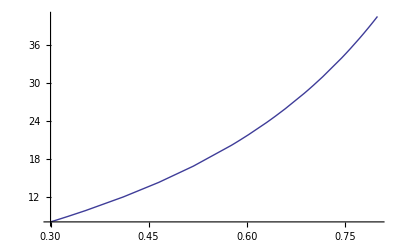

```mathematica
z = Array[0+(#)*(0.010989)&,91]
Plot[  Sum[NIntegrate[((2 + r*Cos[Theta])(2 + r*Cos[Theta]^2 + r*Sin[Theta])^2 - 4*Part[z, i]^2)/(((2 + r*Cos[Theta])^2 + r *Sin[Theta]^2 +Part[z, i]^2)^(7/2)) , {r, 0,t}, {Theta, 0, 2*Pi}], {i, 91}], {t,0.3, 0.8 }, PlotTheme->"Classic", PlotPoints->10, FrameLabel->{"Alpha", "R(cm) of coil"}]
```

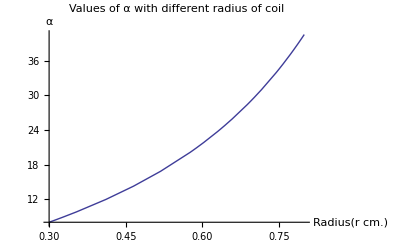

```mathematica
Show[%2,AxesLabel->{RawBoxes[RowBox[{"Radius",RowBox[{"(",RowBox[{"r"," ",RowBox[{"cm","."}]}],")"}]}]],HoldForm[α]},FrameLabel->{{None,None},{None,None}},PlotLabel->HoldForm[Values of α with different radius of coil],LabelStyle->{FontFamily->"Arial",GrayLevel[0],Italic}]
```